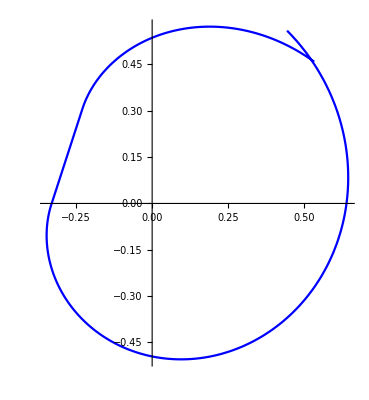

(9-32768 t)/(9-26244 t)

4.71239

5.75959

```mathematica
ClearAll["Global`*"];
getAngle[t_,b_]:=2Pi+Pi/2-2Pi*(t-b^Floor[Log[b,t]])/b^Floor[Log[b,t]];
(*Curve Part 1: t>2^-12: Floor[Log[2,t]=-12], Floor[Log[3,t]]=-8 *)
(*Curve Part 2: t<2^-12: Floor[Log[2,t]=-13], Floor[Log[3,t]]=-8 *)
getAngle2[t_]:=2Pi+Pi/2-2Pi*(t-2^-13)/2^-13;
getAngle3[t_]:=2Pi+Pi/2-2Pi*(t-3^-8)/3^-8;
(*p1[t_]:={Cos[getAngle[t,2]],Sin[getAngle[t,2]]};
p2[t_]:={Cos[getAngle[t,3]],Sin[getAngle[t,3]]};*)

p1[t_]:={Cos[getAngle2[t]],Sin[getAngle2[t]]};
p2[t_]:={Cos[getAngle3[t]],Sin[getAngle3[t]]};
(*m[t_]:=Tan[(getAngle[t,2]+getAngle[t,3])/2];*)
m[t_]:=(p2[t][[2]]-p1[t][[2]])/(p2[t][[1]]-p1[t][[1]]);
f[x_,t_]:=m[t](x-p1[t][[1]])+p1[t][[2]];

(*F[x_,y_,t_]:=(y-p1[t][[2]])(p2[t][[1]]-p1[t][[1]])-(x-p1[t][[1]])(p2[t][[2]]-p1[t][[2]]);
Print[FullSimplify[F[x,y,t]]];*)
F12[x_,y_,t_]:=Cos[13122 π t] (-x+Sin[8192 π t])+Cos[8192 π t] (x-Sin[13122 π t])+y (-Sin[8192 π t]+Sin[13122 π t]);
F13[x_,y_,t_]:=Cos[16384 π t] (x-Sin[13122 π t])+y (Sin[13122 π t]-Sin[16384 π t])+Cos[13122 π t] (-x+Sin[16384 π t]);
F[x_,y_,t_]:=Piecewise[{{F12[x,y,t],t>=2^-12},{F13[x,y,t],t<2^-12}}];
(*Fd[t_]:=D[F[x,y,t],t];
Print[FullSimplify[Fd[t]]];*)
Fd[x_,y_,t_]:=Piecewise[{{-2 π (4096 y Cos[8192 π t]+(-6561 y+2465 Cos[8192 π t]) Cos[13122 π t]+4096 x Sin[8192 π t]+(-6561 x+2465 Sin[8192 π t]) Sin[13122 π t]), 4096 t>1}, {2 π (-8192 y Cos[16384 π t]+Cos[13122 π t] (6561 y+1631 Cos[16384 π t])+6561 x Sin[13122 π t]+(-8192 x+1631 Sin[13122 π t]) Sin[16384 π t]), 4096 t<1}}];
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,3^-8,0.0003},PlotStyle->Blue]
Print[FullSimplify[getAngle2[t]/getAngle3[t]]];
(*ParametricPlot[parametricFunc[t],{t,0.001,2},PlotStyle->Blue]*)
(*Print[FullSimplify[m[t]]];
Print[FullSimplify[x[t]]];
Print[FullSimplify[y[t]]];*)
Print[N[getAngle[3,2]]];
Print[N[getAngle[12,3]]];
(*ParametricPlot[{x[u],y[ u]},{u,1,100}]*)
(*ListPlot[Table[{N[x[u]],N[y[u]]},{u,1,200,2}],Frame->False,Axes->False]*)
```